2) Sea el vector posición r⃗que varia con respecto el tiempo de la siguiente forma.

r⃗(t)=( Cos (ω t - φ), Sin(ω t - φ) )

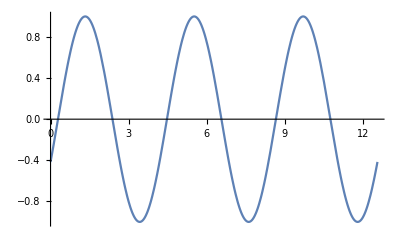

```mathematica
ω=1.5;
R1x = Plot[Cos[ω t-φ]/.φ-> 2,{t,0, 4 Pi}]
```

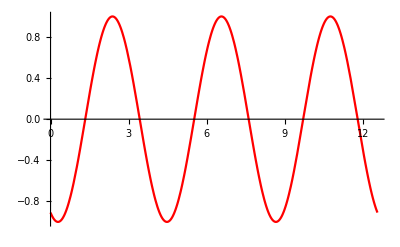

```mathematica
ω=1.5;
R1y = Plot[Sin[ω t-φ]/.φ-> 2,{t,0, 4 Pi}, PlotStyle->Red]
```

La velocidad de las componentes de R esta definida como la derivada con respecto al tiempo de sus componentes entonces tenemos lo siguiente.

OverVector[V(t)]= (d OverVector[r(t)])/dt= d/dt( Cos (ω t-φ),Sin(ω t-φ))= ( (d(Cos (ωt- φ)))/dt,(d(Sin(ω t-φ)))/dt)=. . .
...=(-Sin (ωt-φ)(ωt-φ)/dt ,  Cos(ω t-φ)(ωt- φ)/dt)=(-ω Sin (ωt-φ) ,  ω Cos(ω t-φ))= V⃗(t)

```mathematica
ω=1.5;
V1x=Plot[-Sin[ω t-φ]*ω/. φ->2, {t,0,4 Pi}];
```

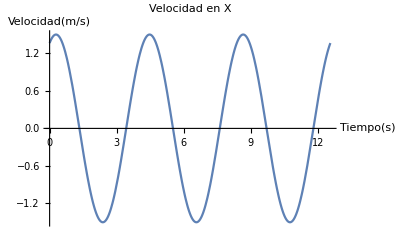

```mathematica
Show[V1x,AxesLabel->{HoldForm[Tiempo[s]],HoldForm[HoldForm[Velocidad[m/s]]]},PlotLabel->"Velocidad en X" ]
```

```mathematica
ω=1.5;
V1y= Plot[Cos[ω t- φ]*ω/. φ->2,{t,0, 4 Pi}, PlotStyle->Red];
```

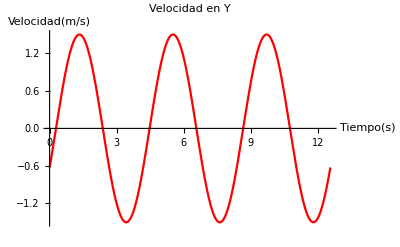

```mathematica
Show[V1y,AxesLabel->{HoldForm[Tiempo[s]],HoldForm[Velocidad[m/s]]},PlotLabel->HoldForm[Velocidad en Y],LabelStyle->{GrayLevel[0]}]
```

Continuamos ahora con la aceleración, tenemos la siguiente formula y desarrollo.

a⃗= (d V⃗)/dt= d/dt(-ω Sin (ωt-φ) ,  ω Cos(ω t-φ))= ( (d(-ω Sin (ωt-φ)))/dt,(d(ω Cos(ω t-φ)))/dt)=(-ω^2 Cos(ω t-φ) ,  ω^2 (- Sin (ωt-φ))= a⃗

```mathematica
ω=1.5;
A1x=Plot[-Cos[ω t-φ]*ω^2/. φ->2, {t,0,4 Pi}];
```

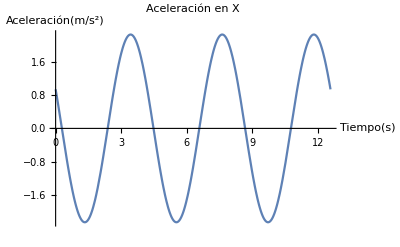

```mathematica
Show[A1x,AxesLabel->{HoldForm[Tiempo[s]],HoldForm[Aceleración[m/s^2]]},PlotLabel->HoldForm[Aceleración en X],LabelStyle->{GrayLevel[0]}]
```

```mathematica
ω=1.5;
A1y=Plot[-Sin[ω t-φ]*ω^2/. φ->2, {t,0,4 Pi},PlotStyle->Red];
```

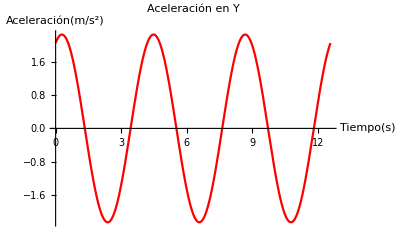

```mathematica
Show[A1y,AxesLabel->{HoldForm[Tiempo[s]],HoldForm[Aceleración[m/s^2]]},PlotLabel->HoldForm[Aceleración en Y],LabelStyle->{GrayLevel[0]}]
```